```mathematica
Im[(1/R+(I*w*Q)^n)^-1]
```

Im[1/(1/R+(ⅈ Q w)^n)]

```mathematica
Refine[ComplexExpand[(1/R+Q*w^n*Exp[Pi/2*n*I])^-1],{Element[R,Reals],Element[n,Integers],Element[w,Integers],Element[Q,Integers], w>0}]
```

1/(R ((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2))+(Q w^n Cos[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)-(ⅈ Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)

```mathematica
Refine[Re[x+I*y],Element[x,Reals]]
```

x-Im[y]

3.29697×10^6

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{{{510.541,{w→3.29697×10^6}}},{□}}

497.899

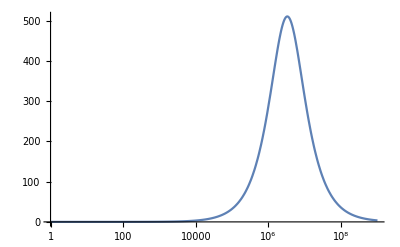

0.000767934

```mathematica
Q=3.416*10^-10;
R=1037.9;
n=0.9896;
1/(R*Q)^(1/n)
{{Maximize[{(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2),w>0},w]}, {□}}
(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)/.w->2621977.4532072237
LogLinearPlot[(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2),{w,1,10^9}, PlotRange->All]
```

```mathematica
ax.set_xlim(-20,1024)
```